### What happens to mean and variance if all the robots past x=b are pushed horizontally back to b? Trying MonteCarlo Analysis Things for Shiva to try: Change the function truncateXTob[b_,input_], to add friction that pulls each particle that hits a wall in the y-direction

```mathematica
{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}}//MatrixForm (*definition of covariance matrix*)
```

(σ_1^2 | ρ σ_1 σ_2
ρ σ_1 σ_2 | σ_2^2)

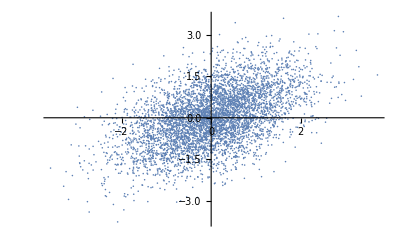

```mathematica
out = RandomVariate[BinormalDistribution[1/2],5000];
ListPlot[out]
```

BinormalDistribution[{μ1, μ2}, {σ1, σ2}, ρ]
represents a bivariate normal distribution with mean {μ_1, μ_2} and covariance matrix {{σ_1^2,ρ σ_1 σ_2},{ρ σ_1 σ_2,σ_2^2}}.

```mathematica
friction[b_,input_,dist_]:=If[input⟦1⟧>b,{b,input⟦2⟧-dist},input]
truncateXTob[b_,input_]:=If[input⟦1⟧>b,{b,input⟦2⟧},input]
truncateXTonb[b_,input_]:=If[input⟦1⟧<b,{b,input⟦2⟧},input]
truncateYToa[a_,input_]:=If[input⟦2⟧>a,{input⟦1⟧,a},input]
```

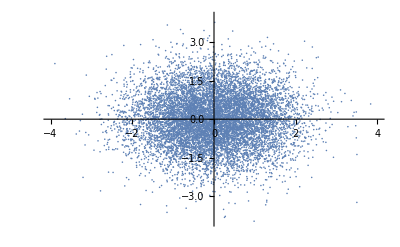

Covariance of data is 0.983217 | 0.00611618
0.00611618 | 1.00197.

Covariance of data is 0.478696 | 0.00119783
0.00119783 | 1.00197, when x_max=1/3

Covariance of data is 0.478696 | 0.000011837
0.000011837 | 0.551123, when x_max=1/3,y_max=1/2

(1.45836 | -0.020064
-0.020064 | 1.96688)

(0.854075 | -0.0143613
-0.0143613 | 1.96688)

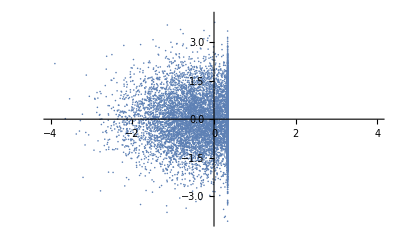

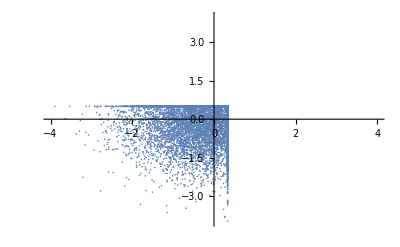

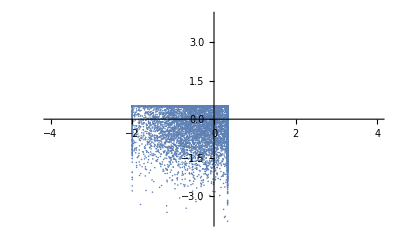

Covariance of data is 0.443628 | -0.0000159571
-0.0000159571 | 0.551123, when x limited to=[-2,1/3,y_max=1/2

```mathematica
n = 10^4;
plotr = 2*{{-2,2},{-2,2}};
pts = RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];
ListPlot[pts,PlotRange->plotr]
b = 1/3;
a = 1/2;
bmin = -2;
ptsx =Map[truncateXTob[b,#]&,pts];
(*ptsx =Map[truncateXTonb[-1,#]&,pts];*)
ptsab =Map[truncateYToa[a,#]&,ptsx];
StringForm["Covariance of data is ``.",Covariance[pts]//MatrixForm]
StringForm["Covariance of data is ``, when x_max=``",Covariance[ptsx]//MatrixForm,b]
StringForm["Covariance of data is ``, when x_max=``,y_max=``",Covariance[ptsab]//MatrixForm,b,a]
ptsxM =ptsx+RandomVariate[BinormalDistribution[{0,0},{1,1},0],n];
ptsBothSifes =Map[ truncateXTonb[bmin,#]&,ptsab];
Covariance[ptsxM]//MatrixForm
ptsxMx =Map[truncateXTob[b,#]&,ptsxM];
Covariance[ptsxMx]//MatrixForm
ListPlot[ptsx,PlotRange->plotr]
ListPlot[ptsab,PlotRange->plotr]
ListPlot[ptsBothSifes,PlotRange->plotr]
StringForm["Covariance of data is ``, when x limited to=[``,``,y_max=``",Covariance[ptsBothSifes]//MatrixForm,bmin,b,a]
```

#### What happens to mean and variance if all the robots past x=b are pushed horizontally back to b? I found an equation for the mean and for the variance. What is the definition of the correlation constant ρ?

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, x],Subscript[μ, y]},({{Subscript[σ, x]^2, ρ Subscript[σ, x] Subscript[σ, y]}, {ρ Subscript[σ, x] Subscript[σ, y], Subscript[σ, y]^2}})],{x,y}]
```

(ⅇ^(1/2 (-((x-μ_x) (y ρ σ_x-ρ μ_y σ_x-x σ_y+μ_x σ_y))/((-1+ρ^2) σ_x^2 σ_y)-((y-μ_y) (-y σ_x+μ_y σ_x+x ρ σ_y-ρ μ_x σ_y))/((-1+ρ^2) σ_x σ_y^2))))/(2 π √(σ_x^2 σ_y^2-ρ^2 σ_x^2 σ_y^2))

```mathematica
∫_b^∞ (ⅇ^(1/2 (-((x-Subscript[μ, x]) (y ρ Subscript[σ, x]-ρ Subscript[μ, y] Subscript[σ, x]-x Subscript[σ, y]+Subscript[μ, x] Subscript[σ, y]))/((-1+ρ^2) Subscript[σ, x]^2 Subscript[σ, y])-((y-Subscript[μ, y]) (-y Subscript[σ, x]+Subscript[μ, y] Subscript[σ, x]+x ρ Subscript[σ, y]-ρ Subscript[μ, x] Subscript[σ, y]))/((-1+ρ^2) Subscript[σ, x] Subscript[σ, y]^2))))/(2 π √(Subscript[σ, x]^2 Subscript[σ, y]^2-ρ^2 Subscript[σ, x]^2 Subscript[σ, y]^2))ⅆx
```

∫_b^∞ (ⅇ^(1/2 (-((x-μ_x) (y ρ σ_x-ρ μ_y σ_x-x σ_y+μ_x σ_y))/((-1+ρ^2) σ_x^2 σ_y)-((y-μ_y) (-y σ_x+μ_y σ_x+x ρ σ_y-ρ μ_x σ_y))/((-1+ρ^2) σ_x σ_y^2))))/(2 π √(σ_x^2 σ_y^2-ρ^2 σ_x^2 σ_y^2))ⅆx

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, x],Subscript[μ, y]},({{Subscript[σ, x]^2, 0}, {0, Subscript[σ, y]^2}})],{x,y}]
```

(ⅇ^(1/2 (-(x-μ_x)^2/σ_x^2-(y-μ_y)^2/σ_y^2)))/(2 π √(σ_x^2 σ_y^2))

```mathematica
(ⅇ^(1/2 (-(x-Subscript[μ, x])^2/Subscript[σ, x]^2-(y-Subscript[μ, y])^2/Subscript[σ, y]^2)))/(2 π √(Subscript[σ, x]^2 Subscript[σ, y]^2))
```

```mathematica
PDF[NormalDistribution[Subscript[μ, x],Subscript[σ, x]],{x}]
```

{(ⅇ^(-(x-μ_x)^2/(2 σ_x^2)))/(√(2 π) σ_x)}

```mathematica
(ⅇ^(-(x-Subscript[μ, x])^2/(2 Subscript[σ, x]^2)))/(√(2 π) Subscript[σ, x])
```

```mathematica
∫_b^∞ (ⅇ^(-x^2/2))/(√(2 π))ⅆx
```

1/2 Erfc[b/(√2)]

```mathematica
PDF[MultinormalDistribution[{0,0},({{Subscript[σ, x]^2, 0}, {0, Subscript[σ, y]^2}})],{x,y}]
```

(ⅇ^(1/2 (-x^2/σ_x^2-y^2/σ_y^2)))/(2 π √(σ_x^2 σ_y^2))

```mathematica
𝒟=ProbabilityDistribution[Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π)), x<b}, {1/2 Erfc[b/(√2)], x==b}, {0, True}}],{x,-∞,∞}];
```

```mathematica
PDF[𝒟,x]
```

Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π)), -b+x<0}, {1/2 Erfc[b/(√2)], -b+x==0}, {0, True}}]

```mathematica
-(ⅇ^(-b^2/2))/(√(2 π))
```

```mathematica
MeanX [b_]:=∫_(-∞)^b x(ⅇ^(-x^2/2))/(√(2 π))ⅆx+b 1/2 Erfc[b/(√2)]
MeanFunc[b_]:=-(ⅇ^(-b^2/2))/(√(2 π))+1/2 b Erfc[b/(√2)](*the solution*)
VarX [b_]:=∫_(-∞)^b x^2(ⅇ^(-x^2/2))/(√(2 π))ⅆx+b 1/2 Erfc[b/(√2)]-MeanFunc[b]^2
VarXFunc[b_]:=1/2 (1-b ⅇ^(-b^2/2) √(2/π)+Erf[b/(√2)]+b Erfc[b/(√2)]-2 ((ⅇ^(-b^2/2))/(√(2 π))-1/2 b Erfc[b/(√2)])^2)
```

```mathematica
meanV =-(ⅇ^(-b^2/2))/(√(2 π))/.{b->1};
PDF[𝒟,x]/.{b->1};

Manipulate[Plot[Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π)), x<b}, {1/2 Erfc[b/(√2)], x==b}, {0, True}}],{x,-4,4},Filling->Axis,Epilog->{
 PointSize[Large],Blue,Line[{{b,0},{b,1/2 Erfc[b/(√2)]}}],Point[{b,1/2 Erfc[b/(√2)]}],
Red,Point[{MeanFunc[b],0}]},PlotRange->{{-4,4},{-.05,1}}],{b,-4,4}]
```

```mathematica
Mean[𝒟]
```

-(ⅇ^(-b^2/2))/(√(2 π))

```mathematica
MeanFunc[b]
```

-(ⅇ^(-b^2/2))/(√(2 π))+1/2 b Erfc[b/(√2)]

```mathematica
Manipulate[Plot[Sin[f x+u],{x,0,2π}],{u, 0 , 2π}, {f, 1,10}]
```